```mathematica
ClearAll[files,importfile,raw]
files=FileNames["*.xlsx",NotebookDirectory[]]
{"/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/8.1/8.1.xlsx","/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/8.1/~$8.1.xlsx"}
importfile=files⟦1⟧
"/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/8.1/8.1.xlsx"
raw = Import[importfile];
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

{/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/1.3/1.3.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/1.3/~$1.3.xlsx}

{/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/8.1/8.1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/8.1/~$8.1.xlsx}

/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/1.3/1.3.xlsx

/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/8.1/8.1.xlsx

## Dataset 1

```mathematica
dataset1 = makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset1simple =raw⟦3⟧⟦2;;⟧
```

{{0.113,0.002},{0.635,0.302},{0.921,0.847},{1.136,1.326},{1.25,1.474},{1.348,1.657},{1.546,1.792},{1.657,1.809},{1.984,1.711},{2.004,1.698},{2.08,1.656},{2.117,1.631},{2.168,1.594},{2.426,1.316},{3.426,0.798},{4.487,0.586},{5.013,0.535},{5.477,0.509},{6.172,0.5},{6.727,0.504},{7.444,0.526},{8.396,0.582},{9.826,0.781},{11.935,1.33}}

## Dataset 2

```mathematica
dataset2 = makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset2simple =raw⟦4⟧⟦2;;⟧
```

{{0.002,0.006},{0.077,0.014},{0.122,0.02},{0.207,0.05},{0.27,0.083},{0.335,0.129},{0.422,0.22},{0.5,0.332},{0.598,0.515},{0.731,0.828},{0.972,1.382},{1.127,1.685},{1.207,1.793},{1.394,1.94},{1.568,1.976},{1.62,1.977},{1.69,1.966},{1.855,1.918},{1.916,1.851},{2.176,1.77},{2.463,1.584},{3.209,1.346},{3.807,1.292},{4.061,1.273},{4.481,1.249},{4.639,1.231},{4.787,1.245},{5.264,1.26},{5.893,1.322},{6.862,1.504},{8.299,1.96},{9.839,2.874},{11.334,4.116}}

```mathematica
Min[dataset1simple⟦All,1⟧]
```

0.113

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

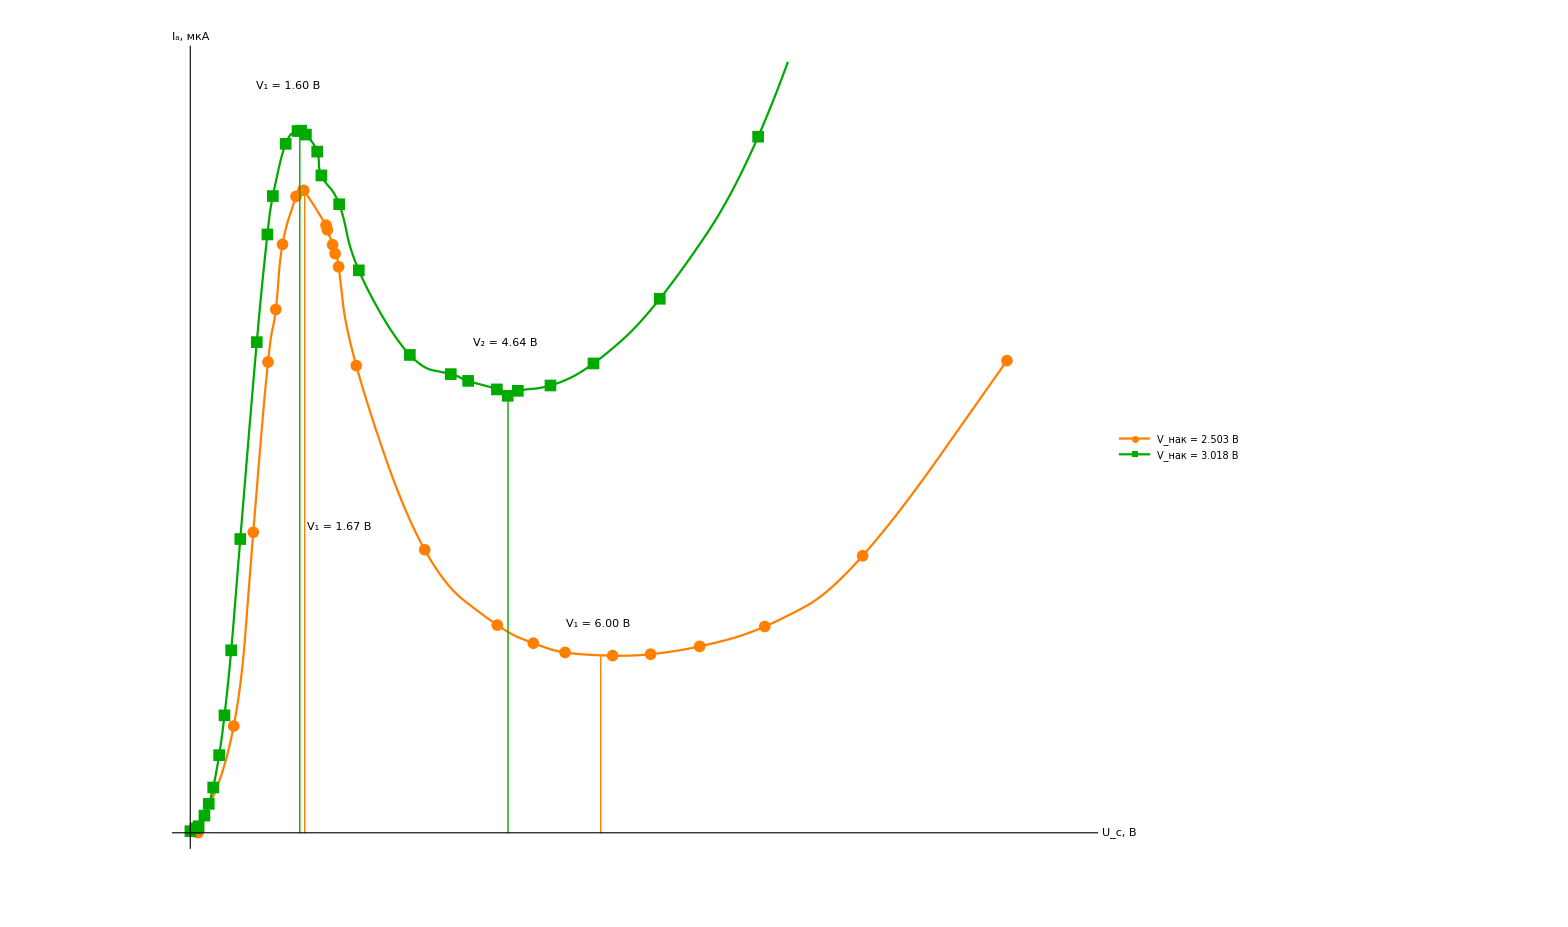

```mathematica
Show[
ListPlot[
{dataset1simple,dataset2simple},
PlotStyle->{Orange,Darker@Green},
Joined->True,
InterpolationOrder->2,
PlotRange-> {{0,13},{0.8Min[dataset1simple⟦All,2⟧],1.2Max[dataset1simple⟦All,2⟧]}},
Ticks-> {Range[-1000,1000, 0.5],Range[-1000,1000, 0.2]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["U_c, В", Large], Style["I_a, мкА", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.5],Range[-1000,1000, 0.05]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
{"V_(:043d:0430:043a) = 2.503 В", "V_(:043d:0430:043a) = 3.018 В"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.8],Scaled[0.84]}
],
Epilog->{
Orange,Line[{{1.6720669897087954,0},{1.6720669897087954,1.809229177257533}}],Line[{{5.998675273180647,0},{5.998675273180647,0.49888323485706415}}],
Darker@Green,Line[{{4.643591431522456,0},{4.643591431522456,1.2309856343040395}}],Line[{{1.6006510776910998,0},{1.6006510776910998,1.9775412361641214}}]
}
],
Graphics[{Black,
Inset[Framed[Style["V_2 = 4.64 В",18],RoundingRadius->10,Background->White],Scaled[{0.36,0.63}]],
Inset[Framed[Style["V_1 = 1.60 В",18],RoundingRadius->10,Background->White],Scaled[{0.125,0.95}]],
Inset[Framed[Style["V_1 = 1.67 В",18],RoundingRadius->10,Background->White],Scaled[{0.18,0.4}]],
Inset[Framed[Style["V_1 = 6.00 В",18],RoundingRadius->10,Background->White],Scaled[{0.46,0.28}]]
}]
]
```

```mathematica
f1= Interpolation[dataset1simple,InterpolationOrder->2]
```

InterpolatingFunction[…]

```mathematica
f2=Interpolation[dataset2simple,InterpolationOrder->2]
```

InterpolatingFunction[…]

```mathematica
FindMinimum[f1[x],{x,4}]
```

{0.498883,{x→5.99868}}

```mathematica
FindMaximum[f1[x],{x,1}]
```

{1.80923,{x→1.67207}}

```mathematica
FindMinimum[f2[x],{x,4}]
```

{1.23099,{x→4.64359}}

```mathematica
FindMaximum[f2[x],{x,1}]
```

{1.97754,{x→1.60065}}

```mathematica
dataset1simple
```

{{0.113,0.002},{0.635,0.302},{0.921,0.847},{1.136,1.326},{1.25,1.474},{1.348,1.657},{1.546,1.792},{1.657,1.809},{1.984,1.711},{2.004,1.698},{2.08,1.656},{2.117,1.631},{2.168,1.594},{2.426,1.316},{3.426,0.798},{4.487,0.586},{5.013,0.535},{5.477,0.509},{6.172,0.5},{6.727,0.504},{7.444,0.526},{8.396,0.582},{9.826,0.781},{11.935,1.33}}

```mathematica
max1= Max[dataset1simple⟦All,2⟧]
```

1.809

```mathematica
max11=-Log[dataset1simple⟦1,2⟧/max1]
```

6.80738

```mathematica
dataset1update ={dataset1simple⟦#⟧⟦1⟧,-Log[dataset1simple⟦#⟧⟦2⟧/max1]/max11}&/@Range[1,Length@dataset1simple]
```

{{0.113,1.},{0.635,0.262965},{0.921,0.111471},{1.136,0.045628},{1.25,0.0300842},{1.348,0.0128927},{1.546,0.00138701},{1.657,0.},{1.984,0.00818174},{2.004,0.00930212},{2.08,0.0129814},{2.117,0.015216},{2.168,0.0185868},{2.426,0.04674},{3.426,0.120225},{4.487,0.165586},{5.013,0.178962},{5.477,0.18628},{6.172,0.188901},{6.727,0.18773},{7.444,0.181454},{8.396,0.166593},{9.826,0.123389},{11.935,0.0451855}}

```mathematica
dataset2simple
```

{{0.002,0.006},{0.077,0.014},{0.122,0.02},{0.207,0.05},{0.27,0.083},{0.335,0.129},{0.422,0.22},{0.5,0.332},{0.598,0.515},{0.731,0.828},{0.972,1.382},{1.127,1.685},{1.207,1.793},{1.394,1.94},{1.568,1.976},{1.62,1.977},{1.69,1.966},{1.855,1.918},{1.916,1.851},{2.176,1.77},{2.463,1.584},{3.209,1.346},{3.807,1.292},{4.061,1.273},{4.481,1.249},{4.639,1.231},{4.787,1.245},{5.264,1.26},{5.893,1.322},{6.862,1.504},{8.299,1.96},{9.839,2.874},{11.334,4.116}}

```mathematica
max2= 1.9775412361641214
```

1.97754

```mathematica
max22=-Log[dataset2simple⟦1,2⟧/max2]
```

5.79785

```mathematica
dataset2update ={dataset2simple⟦#⟧⟦1⟧,-Log[dataset2simple⟦#⟧⟦2⟧/max2]/max22}&/@Range[1,Length@dataset2simple-2]
```

{{0.002,1.},{0.077,0.85386},{0.122,0.792342},{0.207,0.634302},{0.27,0.546887},{0.335,0.470829},{0.422,0.378758},{0.5,0.307782},{0.598,0.232059},{0.731,0.150158},{0.972,0.0618027},{1.127,0.0276117},{1.207,0.0168966},{1.394,0.00330576},{1.568,0.000134476},{1.62,0.0000472121},{1.69,0.00100956},{1.855,0.00527287},{1.916,0.0114056},{2.176,0.0191234},{2.463,0.038273},{3.209,0.0663551},{3.807,0.0734174},{4.061,0.0759726},{4.481,0.0792554},{4.639,0.0817592},{4.787,0.0798087},{5.264,0.0777431},{5.893,0.0694583},{6.862,0.0472116},{8.299,0.00153674}}

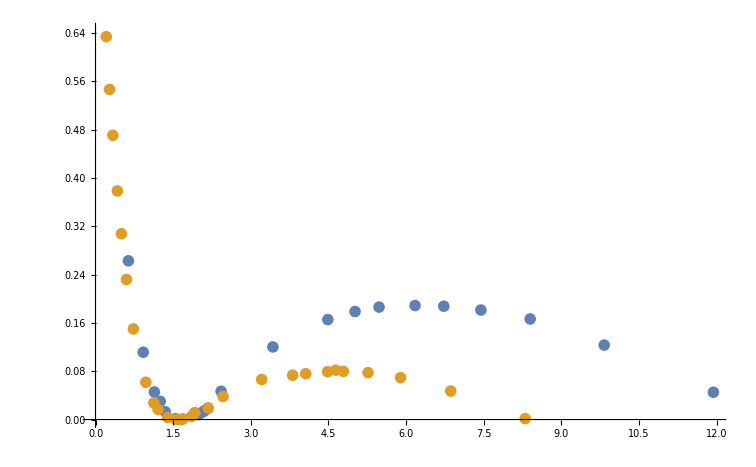

```mathematica
ListPlot[{dataset1update,dataset2update}]
```

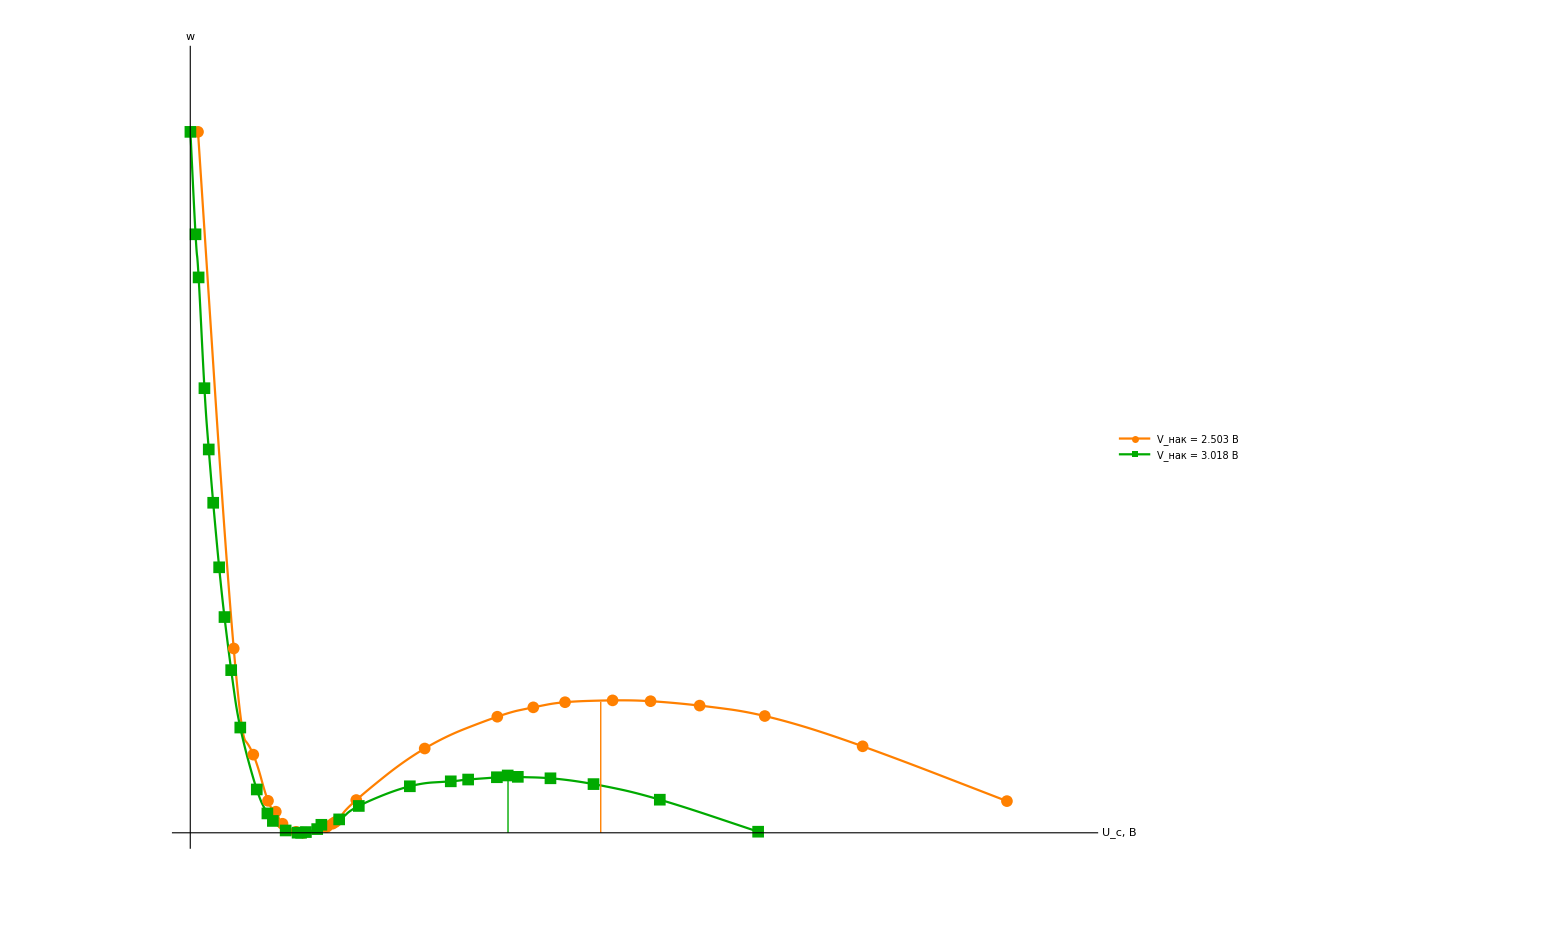

```mathematica
Show[
ListPlot[
{dataset1update,dataset2update},
PlotStyle->{Orange,Darker@Green},
Joined->True,
InterpolationOrder->2,
PlotRange-> {{0,13},{0,1.1}},
Ticks-> {Range[-1000,1000, 0.5],Range[-1000,1000, 0.2]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["U_c, В", Large], Style["w", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.5],Range[-1000,1000, 0.05]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
{"V_(:043d:0430:043a) = 2.503 В", "V_(:043d:0430:043a) = 3.018 В"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.5],Scaled[0.65]}
],
Epilog->{
Orange,(*Line[{{1.6720669897087954,0},{1.6720669897087954,1.809229177257533}}],*)Line[{{5.998675273180647,0},{5.998675273180647,0.187}}],
Darker@Green,Line[{{4.643591431522456,0},{4.643591431522456,0.08}}](*,Line[{{1.6006510776910998,0},{1.6006510776910998,1.9775412361641214}}]*)
}
](*,*)
(*Graphics[{Black,
Inset[Framed[Style["V_2 = 4.64 В",18],RoundingRadius->10,Background->White],Scaled[{0.36,0.63}]],
Inset[Framed[Style["V_1 = 1.60 В",18],RoundingRadius->10,Background->White],Scaled[{0.125,0.95}]],
Inset[Framed[Style["V_1 = 1.67 В",18],RoundingRadius->10,Background->White],Scaled[{0.18,0.4}]],
Inset[Framed[Style["V_1 = 6.00 В",18],RoundingRadius->10,Background->White],Scaled[{0.46,0.28}]]
}]*)
]
```